```mathematica
QuantumGroupsPath = "c:\\scott\\projects\\QuantumGroups\\trunk\\package\\";
AppendTo[$Path, QuantumGroupsPath];
<<QuantumGroups`
```

Loading QuantumGroups` version 2.0
Read more at http://katlas.math.toronto.edu/wiki/QuantumGroups

Found precomputed data in C:\scott\projects\QuantumGroups\trunk\data

General::obspkg: "LinearAlgebra`MatrixManipulation`" is now obsolete. The legacy version being loaded may conflict with current Mathematica functionality. See the Compatibility Guide for updating information.

```mathematica
qDimension[A1][Irrep[A1][{1}]]
```

1/q+q

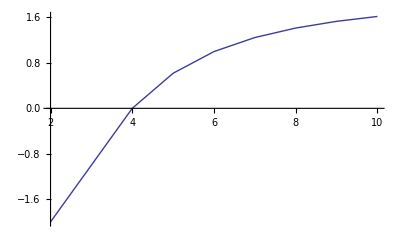

```mathematica
ListPlot[Table[{k,qDimension[A1][Irrep[A1][{1}]]/.q->ⅇ^((2π ⅈ)/k)},{k,2,10}],"PlotJoined"->True]
```

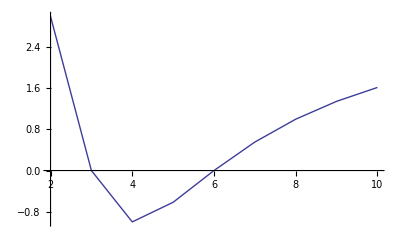

```mathematica
ListPlot[Table[{k,qDimension[A2][Irrep[A2][{1,0}]]/.q->ⅇ^((2π ⅈ)/k)},{k,2,10}],"PlotJoined"->True]
```

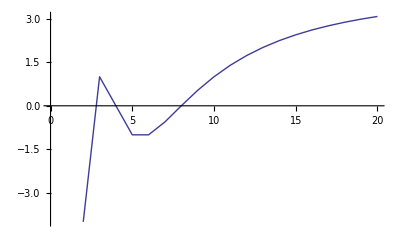

```mathematica
ListPlot[Table[{k,qDimension[A3][Irrep[A3][{1,0,0}]]/.q->ⅇ^((2π ⅈ)/k)},{k,2,20}],"PlotJoined"->True]
```

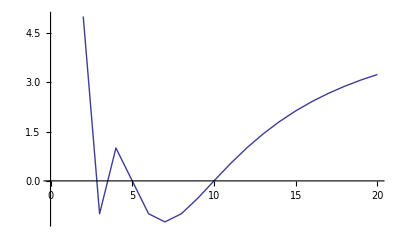

```mathematica
ListPlot[Table[{k,qDimension[A4][Irrep[A4][{1,0,0,0}]]/.q->ⅇ^((2π ⅈ)/k)},{k,2,20}],"PlotJoined"->True]
```

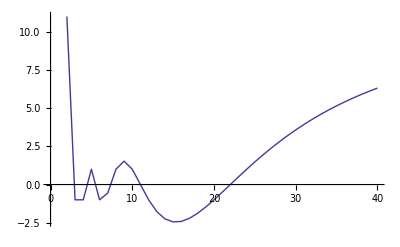

```mathematica
ListPlot[Table[{k,qDimension[Subscript[A, 10]][Irrep[Subscript[A, 10]][UnitVector[10,1]]]/.q->ⅇ^((2π ⅈ)/k)},{k,2,40}],"PlotJoined"->True]
```

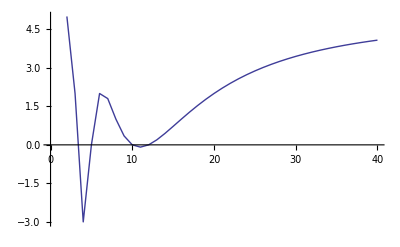

```mathematica
ListPlot[Table[{k,qDimension[Subscript[B, 2]][Irrep[Subscript[B, 2]][UnitVector[2,1]]]/.q->ⅇ^((2π ⅈ)/k)},{k,2,40}],"PlotJoined"->True]
```

```mathematica
DualCoxeterNumber[Subscript[A, k]]
```

1+k

```mathematica
DualCoxeterNumber[Subscript[B, k]]
```

-1+2 k

```mathematica
Table[FullSimplify[qDimension[Subscript[A, k]][Irrep[Subscript[A, k]][UnitVector[k,1]]]/.q->ⅇ^((2π ⅈ)/(2DualCoxeterNumber[Subscript[A, k]]))],{k,1,10}]
```

{0,0,0,0,0,0,0,0,0,0}

```mathematica
Table[Chop[N[qDimension[Subscript[A, k]][Irrep[Subscript[A, k]][UnitVector[k,1]]]/.q->ⅇ^((2π ⅈ)/(2DualCoxeterNumber[Subscript[A, k]]+1))]],{k,1,10}]
```

{0.618034,0.554958,0.532089,0.521109,0.514964,0.51117,0.508661,0.506914,0.505648,0.504701}

```mathematica
Table[Chop[N[qDimension[Subscript[A, k]][Irrep[Subscript[A, k]][UnitVector[k,1]]]/.q->ⅇ^((2π ⅈ)/(2(DualCoxeterNumber[Subscript[A, k]]+1)))]],{k,1,10}]
```

{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

```mathematica
Table[FullSimplify[qDimension[Subscript[B, k]][Irrep[Subscript[B, k]][UnitVector[k,1]]]/.q->ⅇ^((2π ⅈ)/(4DualCoxeterNumber[Subscript[B, k]]))],{k,2,6}]
```

{0,0,0,0,0}

```mathematica
Table[Chop[N[qDimension[Subscript[B, k]][Irrep[Subscript[B, k]][UnitVector[k,1]]]/.q->ⅇ^((2π ⅈ)/(4(DualCoxeterNumber[Subscript[B, k]]+1)))]],{k,2,6}]
```

{1.,1.,1.,1.,1.}

```mathematica
md[Γ_,l_]:=Re[qDimension[Γ][Irrep[Γ][UnitVector[Rank[Γ],1]]]/.q->Exp[(2π ⅈ)/(2Max[CartanFactors[Γ]](DualCoxeterNumber[Γ]+l))]]
```

```mathematica
N[Table[md[A1,l],{l,1,20}]]
```

{1.,1.41421,1.61803,1.73205,1.80194,1.84776,1.87939,1.90211,1.91899,1.93185,1.94188,1.94986,1.9563,1.96157,1.96595,1.96962,1.97272,1.97538,1.97766,1.97964}

```mathematica
N[Table[md[A2,l],{l,1,20}]]
```

{1.,1.61803,2.,2.24698,2.41421,2.53209,2.61803,2.68251,2.73205,2.77091,2.80194,2.82709,2.84776,2.86494,2.87939,2.89163,2.90211,2.91115,2.91899,2.92583}

```mathematica
N[Table[md[A3,l],{l,1,20}]]
```

{1.,1.73205,2.24698,2.61313,2.87939,3.07768,3.22871,3.34607,3.43891,3.51352,3.57433,3.62451,3.66638,3.70167,3.73167,3.75739,3.7796,3.79891,3.81579,3.83065}

```mathematica
N[Table[md[A4,l],{l,1,20}]]
```

{1.,1.80194,2.41421,2.87939,3.23607,3.51334,3.73205,3.90704,4.04892,4.16535,4.26197,4.34296,4.41147,4.46992,4.52015,4.56362,4.60149,4.63467,4.6639,4.68978}

```mathematica
N[Table[md[B2,l],{l,1,20}]]
```

{1.,2.,2.73205,3.24698,3.61313,3.87939,4.07768,4.22871,4.34607,4.43891,4.51352,4.57433,4.62451,4.66638,4.70167,4.73167,4.75739,4.7796,4.79891,4.81579}

```mathematica
N[Table[md[B3,l],{l,1,20}]]
```

{1.,2.,2.84776,3.53209,4.07768,4.51334,4.8637,5.14811,5.38129,5.57433,5.73565,5.87165,5.98724,6.08623,6.1716,6.2457,6.31041,6.36722,6.41736,6.46182}

```mathematica
N[Table[md[B4,l],{l,1,20}]]
```

{1.,2.,2.90211,3.68251,4.34607,4.90704,5.38129,5.78339,6.12583,6.41898,6.67128,6.88962,7.07958,7.2457,7.39169,7.52058,7.63488,7.73666,7.82766,7.90932}

```mathematica
N[Table[md[C3,l],{l,1,20}]]
```

{1.61803,2.73205,3.49396,4.02734,4.41147,4.69572,4.91121,5.07812,5.20982,5.31546,5.40142,5.47227,5.53132,5.58105,5.6233,5.6595,5.69074,5.71789,5.74163,5.7625}

```mathematica
N[Table[md[C4,l],{l,1,20}]]
```

{1.73205,3.04892,4.02734,4.75877,5.31375,5.74204,6.07812,6.34595,6.56244,6.73968,6.88648,7.00934,7.11314,7.20159,7.27754,7.34322,7.4004,7.45047,7.49455,7.53356}

```mathematica
N[Table[md[D4,l],{l,1,20}]]
```

{1.,2.,2.87939,3.61803,4.22871,4.73205,5.14811,5.49396,5.78339,6.02734,6.23444,6.41147,6.56381,6.69572,6.8106,6.91121,6.99978,7.07812,7.14772,7.20982}

```mathematica
N[Table[md[E6,l],{l,1,20}]]
```

{1.,2.24698,3.61803,5.02734,6.41898,7.75877,9.02751,10.2159,11.3209,12.3435,13.2871,14.1562,14.956,15.6919,16.3691,16.9926,17.5673,18.0974,18.587,19.0397}

```mathematica
N[Table[md[E7,l],{l,1,20}]]
```

{-8.88178×10^-16,1.61803,3.79129,6.43232,9.44641,12.742,16.2364,19.858,23.5468,27.2541,30.9408,34.5768,38.1387,41.6096,44.9772,48.2333,51.3728,54.393,57.2932,60.0742}

```mathematica
N[Table[md[E8,l],{l,1,20}]]
```

{1.42109×10^-14,1.,3.51334,8.00934,14.8869,24.46,36.9539,52.507,71.1782,92.9572,117.775,145.515,176.023,209.121,244.607,282.273,321.902,363.277,406.187,450.424}

```mathematica
N[Table[md[F4,l],{l,1,20}]]
```

{0.,1.91899,4.44949,7.30219,10.2614,13.1848,15.9865,18.6203,21.0654,23.3173,25.3808,27.266,28.9857,30.5534,31.9829,33.287,34.478,35.5671,36.5642,37.4786}

```mathematica
N[Table[md[G2,l],{l,1,20}]]
```

{1.61803,2.87939,3.79129,4.44949,4.93257,5.29456,5.57144,5.78728,5.95843,6.09624,6.20872,6.30165,6.37926,6.44472,6.50041,6.54819,6.58946,6.62535,6.65676,6.68439}

```mathematica
With[{Γ=A2,l=3},Table[Chop[N[qDimension[Γ][Irrep[Γ][{a,b}]]/.q->Exp[(2π ⅈ)/(2Max[CartanFactors[Γ]](DualCoxeterNumber[Γ]+l))]]],{a,0,4},{b,0,4}]]//TableForm
```

1. | 2. | 2. | 1. | 0
2. | 3. | 2. | 0 | -1.
2. | 2. | 0 | -2. | -2.
1. | 0 | -2. | -3. | -2.
0 | -1. | -2. | -2. | -1.

```mathematica
ρ[Γ_]:=(Plus@@PositiveRoots[Γ])/2
```

```mathematica
ρ[G2]
```

{1,1}

So it looks like when <ρ,λ> = l+1, the dimension is zero?

```mathematica
KillingForm[A2][ρ[A2],{2,3}]
```

5

```mathematica
With[{Γ=A3,l=3},Table[Chop[N[qDimension[Γ][Irrep[Γ][{a,b,c}]]/.q->Exp[(2π ⅈ)/(2Max[CartanFactors[Γ]](DualCoxeterNumber[Γ]+l))]]],{a,0,2},{b,0,2},{c,0,2}]]
```

{{{1.,2.24698,2.24698},{2.80194,4.04892,2.24698},{2.80194,2.24698,0}},{{2.24698,4.04892,2.80194},{4.04892,4.04892,0},{2.24698,0,-2.24698}},{{2.24698,2.80194,0},{2.24698,0,-4.04892},{0,-2.24698,-2.80194}}}

```mathematica
With[{Γ=A3,l=2},Cases[Flatten[Table[{a,b,c},{a,0,2},{b,0,2},{c,0,2}],2],{a_,b_,c_}/;(Chop[N[qDimension[Γ][Irrep[Γ][{a,b,c}]]/.q->Exp[(2π ⅈ)/(2Max[CartanFactors[Γ]](DualCoxeterNumber[Γ]+l))]]]==0)]]
```

{{0,1,2},{0,2,1},{0,2,2},{1,0,2},{1,1,1},{1,2,0},{1,2,2},{2,0,1},{2,1,0},{2,2,0},{2,2,1},{2,2,2}}

```mathematica
KillingForm[A3][ρ[A3],#]&/@%
```

{5,11/2,7,9/2,5,11/2,17/2,9/2,5,7,17/2,10}

```mathematica
Table[KillingForm[A3][ρ[A3],{a,b,c}],{a,0,2},{b,0,2},{c,0,2}]
```

{{{0,3/2,3},{2,7/2,5},{4,11/2,7}},{{3/2,3,9/2},{7/2,5,13/2},{11/2,7,17/2}},{{3,9/2,6},{5,13/2,8},{7,17/2,10}}}

```mathematica
With[{Γ=A3,l=3},Cases[Flatten[Table[{a,b,c},{a,0,3},{b,0,3},{c,0,3}],2],{a_,b_,c_}/;(Chop[N[qDimension[Γ][Irrep[Γ][{a,b,c}]]/.q->Exp[(2π ⅈ)/(2Max[CartanFactors[Γ]](DualCoxeterNumber[Γ]+l))]]]==0)]]
```

{{0,1,3},{0,2,2},{0,2,3},{0,3,1},{0,3,2},{1,0,3},{1,1,2},{1,2,1},{1,2,3},{1,3,0},{1,3,2},{2,0,2},{2,1,1},{2,2,0},{2,2,3},{2,3,0},{2,3,1},{2,3,2},{2,3,3},{3,0,1},{3,1,0},{3,2,0},{3,2,1},{3,2,2},{3,2,3},{3,3,2}}

```mathematica
Min[KillingForm[A3][ρ[A3],#]&/@%]
```

6

```mathematica
With[{Γ=A3,l=4},Cases[Flatten[Table[{a,b,c},{a,0,3},{b,0,3},{c,0,3}],2],{a_,b_,c_}/;(Chop[N[qDimension[Γ][Irrep[Γ][{a,b,c}]]/.q->Exp[(2π ⅈ)/(2Max[CartanFactors[Γ]](DualCoxeterNumber[Γ]+l))]]]==0)]]
```

{{0,2,3},{0,3,2},{0,3,3},{1,1,3},{1,2,2},{1,3,1},{1,3,3},{2,0,3},{2,1,2},{2,2,1},{2,3,0},{2,3,3},{3,0,2},{3,1,1},{3,2,0},{3,3,0},{3,3,1},{3,3,2},{3,3,3}}

```mathematica
Min[KillingForm[A3][ρ[A3],#]&/@%]
```

15/2

```mathematica
With[{Γ=A3,l=5},Cases[Flatten[Table[{a,b,c},{a,0,3},{b,0,3},{c,0,3}],2],{a_,b_,c_}/;(Chop[N[qDimension[Γ][Irrep[Γ][{a,b,c}]]/.q->Exp[(2π ⅈ)/(2Max[CartanFactors[Γ]](DualCoxeterNumber[Γ]+l))]]]==0)]]
```

{{0,3,3},{1,2,3},{1,3,2},{2,1,3},{2,2,2},{2,3,1},{3,0,3},{3,1,2},{3,2,1},{3,3,0}}

```mathematica
Min[KillingForm[A3][ρ[A3],#]&/@%]
```

9

```mathematica
9/2,6,15/2,9
```

<ρ, λ > = 3/2(l + 1)

```mathematica
DualCoxeterNumber[Subscript[A, n]]
```

1+n

```mathematica
DualCoxeterNumber[Subscript[B, n]]
```

-1+2 n

```mathematica
With[{Γ=B2,l=3},Table[Chop[N[qDimension[Γ][Irrep[Γ][{a,b}]]/.q->Exp[(2π ⅈ)/(2Max[CartanFactors[Γ]](DualCoxeterNumber[Γ]+l))]]],{a,0,4},{b,0,4}]]//TableForm
```

1. | 2.73205 | 3.73205 | 2.73205 | 0
2.73205 | 4.73205 | 3.73205 | 0 | -3.73205
2.73205 | 2.73205 | 0 | -2.73205 | -2.73205
1. | 0 | -1. | 0 | 2.73205
0 | 0 | 1. | 2.73205 | 3.73205

```mathematica
KillingForm[B2][ρ[B2],{4,0}]
```

12

```mathematica
With[{Γ=B2,l=4},Table[Chop[N[qDimension[Γ][Irrep[Γ][{a,b}]]/.q->Exp[(2π ⅈ)/(2Max[CartanFactors[Γ]](DualCoxeterNumber[Γ]+l))]]],{a,0,4},{b,0,4}]]//TableForm
```

1. | 3.04892 | 5.04892 | 5.49396 | 3.60388
3.24698 | 6.85086 | 8.09783 | 5.49396 | 0
4.49396 | 6.85086 | 5.04892 | 0 | -5.04892
3.24698 | 3.04892 | 0 | -3.04892 | -3.24698
1. | 0 | -1. | 0 | 3.24698

```mathematica
KillingForm[B2][ρ[B2],{5,0}]
```

15

Now <ρ,λ> =3(l+1).

```mathematica
With[{Γ=B3,l=1},Cases[Flatten[Table[{a,b,c},{a,0,2},{b,0,2},{c,0,2}],2],{a_,b_,c_}/;(Chop[N[qDimension[Γ][Irrep[Γ][{a,b,c}]]/.q->Exp[(2π ⅈ)/(2Max[CartanFactors[Γ]](DualCoxeterNumber[Γ]+l))]]]==0)]]
```

{{0,0,2},{0,1,0},{0,1,2},{0,2,1},{0,2,2},{1,0,1},{1,0,2},{1,1,1},{1,2,0},{1,2,1},{1,2,2},{2,0,0},{2,0,1},{2,1,0},{2,1,1},{2,2,0},{2,2,1},{2,2,2}}

```mathematica
Min[KillingForm[B3][ρ[B3],#]&/@%]
```

8

```mathematica
With[{Γ=B3,l=2},Cases[Flatten[Table[{a,b,c},{a,0,3},{b,0,2},{c,0,2}],2],{a_,b_,c_}/;(Chop[N[qDimension[Γ][Irrep[Γ][{a,b,c}]]/.q->Exp[(2π ⅈ)/(2Max[CartanFactors[Γ]](DualCoxeterNumber[Γ]+l))]]]==0)]]
```

{{0,1,1},{0,2,2},{1,0,2},{1,1,0},{1,1,2},{1,2,1},{2,0,1},{2,0,2},{2,1,1},{2,2,0},{2,2,1},{3,0,0},{3,0,1},{3,1,0},{3,1,1},{3,2,0},{3,2,1},{3,2,2}}

```mathematica
Min[KillingForm[B3][ρ[B3],#]&/@%]
```

25/2

```mathematica
With[{Γ=B3,l=3},Cases[Flatten[Table[{a,b,c},{a,0,3},{b,0,2},{c,0,2}],2],{a_,b_,c_}/;(Chop[N[qDimension[Γ][Irrep[Γ][{a,b,c}]]/.q->Exp[(2π ⅈ)/(2Max[CartanFactors[Γ]](DualCoxeterNumber[Γ]+l))]]]==0)]]
```

{{0,1,2},{0,2,0},{1,1,1},{1,2,2},{2,0,2},{2,1,0},{2,1,2},{2,2,1},{3,0,1},{3,0,2},{3,1,1},{3,2,0},{3,2,1}}

```mathematica
Min[KillingForm[B3][ρ[B3],#]&/@%]
```

16

```mathematica
With[{Γ=B3,l=4},Cases[Flatten[Table[{a,b,c},{a,0,3},{b,0,2},{c,0,2}],2],{a_,b_,c_}/;(Chop[N[qDimension[Γ][Irrep[Γ][{a,b,c}]]/.q->Exp[(2π ⅈ)/(2Max[CartanFactors[Γ]](DualCoxeterNumber[Γ]+l))]]]==0)]]
```

{{0,2,1},{1,1,2},{1,2,0},{2,1,1},{2,2,2},{3,0,2},{3,1,0},{3,1,2},{3,2,1}}

```mathematica
Min[KillingForm[B3][ρ[B3],#]&/@%]
```

41/2

Now <ρ,λ> = 4 (l + 1).

```mathematica
Table[KillingForm[B3][ρ[B3],{a,b,c}],{a,0,3},{b,0,2},{c,0,2}]
```

{{{0,9/2,9},{8,25/2,17},{16,41/2,25}},{{5,19/2,14},{13,35/2,22},{21,51/2,30}},{{10,29/2,19},{18,45/2,27},{26,61/2,35}},{{15,39/2,24},{23,55/2,32},{31,71/2,40}}}

```mathematica
With[{Γ=G2},Table[KillingForm[G2][ρ[G2],{a,b}],{a,0,4},{b,0,4}]]//TableForm
```

0 | 9 | 18 | 27 | 36
5 | 14 | 23 | 32 | 41
10 | 19 | 28 | 37 | 46
15 | 24 | 33 | 42 | 51
20 | 29 | 38 | 47 | 56

```mathematica
32,27,23,18,14,9
```

Now <ρ, λ> = 9/2(l+1).

```mathematica
With[{Γ=G2,l=1},Table[Chop[N[qDimension[Γ][Irrep[Γ][{a,b}]]/.q->Exp[(2π ⅈ)/(2Max[CartanFactors[Γ]](DualCoxeterNumber[Γ]+l))]]],{a,0,4},{b,0,4}]]//TableForm
```

1. | 0 | -1. | 0 | 0
1.61803 | -1.61803 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 1. | 0 | -1. | 0
1.61803 | -1. | 1. | -1.61803 | 0

```mathematica
With[{Γ=G2,l=2},Table[Chop[N[qDimension[Γ][Irrep[Γ][{a,b}]]/.q->Exp[(2π ⅈ)/(2Max[CartanFactors[Γ]](DualCoxeterNumber[Γ]+l))]]],{a,0,4},{b,0,4}]]//TableForm
```

1. | 1.87939 | -1.87939 | -1. | 0
2.87939 | 0 | -2.87939 | 0 | 0
2.53209 | -2.53209 | 0 | 0 | 0
0 | 0 | 1. | 0 | -1.
0 | 2.87939 | -1. | 1. | -2.87939

```mathematica
With[{Γ=G2,l=3},Table[Chop[N[qDimension[Γ][Irrep[Γ][{a,b}]]/.q->Exp[(2π ⅈ)/(2Max[CartanFactors[Γ]](DualCoxeterNumber[Γ]+l))]]],{a,0,4},{b,0,4}]]//TableForm
```

1. | 3.79129 | 0 | -3.79129 | -1.
3.79129 | 4.79129 | -4.79129 | -3.79129 | 0
5.79129 | 0 | -5.79129 | 0 | 0
3.79129 | -3.79129 | 0 | 1. | 0
0 | 0 | 3.79129 | -1. | 1.

```mathematica
With[{Γ=G2,l=4},Table[Chop[N[qDimension[Γ][Irrep[Γ][{a,b}]]/.q->Exp[(2π ⅈ)/(2Max[CartanFactors[Γ]](DualCoxeterNumber[Γ]+l))]]],{a,0,4},{b,0,4}]]//TableForm
```

1. | 5.44949 | 4.44949 | -4.44949 | -5.44949
4.44949 | 10.899 | 0 | -10.899 | -4.44949
8.89898 | 8.89898 | -8.89898 | -8.89898 | 0
9.89898 | 0 | -9.89898 | 0 | 1.
5.44949 | -5.44949 | 0 | 4.44949 | -1.

```mathematica
With[{Γ=G2,l=5},Table[Chop[N[qDimension[Γ][Irrep[Γ][{a,b}]]/.q->Exp[(2π ⅈ)/(2Max[CartanFactors[Γ]](DualCoxeterNumber[Γ]+l))]]],{a,0,4},{b,0,4}]]//TableForm
```

1. | 6.81195 | 10.2702 | 0 | -10.2702
4.93257 | 17.0821 | 11.8023 | -11.8023 | -17.0821
11.5857 | 21.774 | 0 | -21.774 | -11.5857
16.7348 | 14.3691 | -14.3691 | -16.7348 | 0
15.3691 | 0 | -15.3691 | 0 | 4.93257

```mathematica
With[{Γ=G2,l=6},Table[Chop[N[qDimension[Γ][Irrep[Γ][{a,b}]]/.q->Exp[(2π ⅈ)/(2Max[CartanFactors[Γ]](DualCoxeterNumber[Γ]+l))]]],{a,0,4},{b,0,4}]]//TableForm
```

1. | 7.91259 | 16.4794 | 9.56677 | -9.56677
5.29456 | 22.7739 | 28.2822 | 0 | -28.2822
13.8252 | 36.1948 | 22.3696 | -22.3696 | -36.1948
23.392 | 36.849 | 0 | -36.849 | -23.392
27.6642 | 21.3696 | -21.3696 | -27.6642 | 0